```mathematica
SetDirectory[NotebookDirectory[]];
li=Import["动画区收藏数据.csv",CharacterEncoding-> "CP936"];
Dimensions@li
```

{32,9}

```mathematica
f=Interpolation[li⟦2;;-1,2⟧, Method->"Spline"];
```

```mathematica
g=Interpolation[li⟦2;;-1,2⟧,InterpolationOrder->1];
```

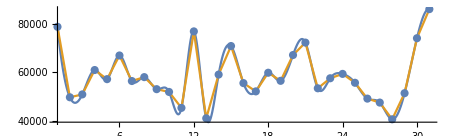

```mathematica
Show[Plot[{f[x],g[x]},{x,1,31},AspectRatio->.3],ListPlot[li⟦2;;-1,2⟧]]
```

### 通过样条插值增加10倍数据量

```mathematica
lip=Table[Interpolation[li⟦2;;-1,y+1⟧, Method->"Spline"][x],{x,1,31.9,0.1},{y,8}];
Dimensions@lip
```

{310,8}

```mathematica
lip=ArrayFlatten[{{
Table[{li⟦Floor@j+1,1⟧},{j,1,31.9,0.1}],
lip
}}] ;
```

```mathematica
Export["lip.csv",lip,CharacterEncoding-> "CP936"];
```